## Independend copula

```mathematica
Plot3D[x y,{x,0,1},{y,0,1},PlotRange->{0,1},BoxRatios->{1,1,0.6}]
```

-Graphics3D-

```mathematica
SeedRandom[];
```

```mathematica
U={};
For[i=0,i<10000,i++,
X=RandomReal[];
Y=RandomReal[];
AppendTo[U,{X,Y}]]
```

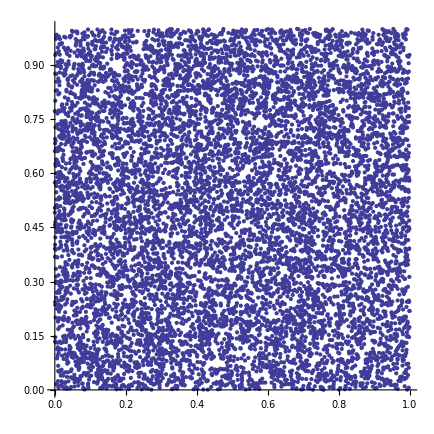

```mathematica
ListPlot[U,AspectRatio->1]
```

```mathematica
F[a_,b_]:=10000-Sort[Tally[UnitStep[a-#1[[2]]]UnitStep[b-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&][[1,2]]
```

```mathematica
Sort[Tally[UnitStep[20/20-#1[[2]]]UnitStep[20/20-#1[[1]]]&/@U],#1[[1]]<#2[[1]]&]
```

{{1,10000}}

```mathematica
n=40;G={};
For[i=0,i<n,i++,
For[j=0,j<n,j++,
AppendTo[G,{i/n,j/n,F[i/n,j/n]}];
]]
```

```mathematica
G[[3]]
```

{0,1/10,0}

```mathematica
ListPlot3D[G,PlotRange->All,BoxRatios->{1,1,1}]
```

-Graphics3D-